```mathematica
LogNormal[x_,μ_,σ_]:=1/(σ x √(2 Pi)) Exp[-(Log[x]-μ)^2/(2 σ^2)]
NormalDist[x_,μ_,σ_]:=1/√(2 Pi σ^2) Exp[-(x-μ)^2/(2 σ^2)]
```

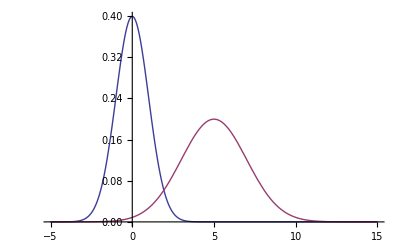

```mathematica
Plot[{NormalDist[x,0,1],NormalDist[x,5,2]},{x,-5,15},PlotRange->{Automatic,Full}]
```

```mathematica
FindRoot[NormalDist[x,0,1]==NormalDist[x,5,2],{x,1}]
```

{x→1.93326}

```mathematica
1-(NIntegrate[0.5*NormalDist[x,5,2],{x,-Infinity,1.93326}]+NIntegrate[0.5*NormalDist[x,0,1],{x,1.93326,Infinity}])
```

0.955403

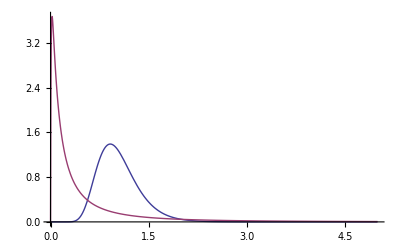

```mathematica
Plot[{LogNormal[x,0,0.3],LogNormal[x,-1.5,1.5]},{x,0,5},PlotRange->{Automatic,Full}]
```

```mathematica
FindRoot[LogNormal[x,0,0.3]==LogNormal[x,-1.5,1.5],{x,0.2}]
```

{x→0.565807}

```mathematica
1-(NIntegrate[0.5*LogNormal[x,0,0.3],{x,0,0.565807}]+NIntegrate[0.5*LogNormal[x,-1.5,1.5],{x,0.565807,Infinity}])
```

0.851827

```mathematica
1-0.147
```

0.853

```mathematica
1-0.12
```

0.88